Evaluation>Evaluate Notebook

```mathematica
$H="/Volumes/World/Users/latur/Public/DREAM6/r-code/";
FN[pattern_]:=FileNames[pattern,$H<>"results/",2];
```

```mathematica
(* Чтение файла известных параметров, преобразование в список *)
P=StringCases[
StringReplace[Import[#],"\n"->","],
RegularExpression["=([0-9.]{1,10})"]->"$1"
]&/@FileNames["parms.txt",$H,∞]//ToExpression;
```

```mathematica
(* График значений функционала *)
FValue[list_]:={#⟦1⟧,#⟦3⟧}&/@list;
```

```mathematica
(* График значений расстояния между параметрами *)
Distance[pred_,real_]:=Total[Log[pred/real⟦1;;Length[pred]⟧]^2]/Length[pred];
PValue[list_,p_]:={#⟦1⟧,Distance[#⟦4;;-1⟧,p]}&/@list;
```

```mathematica
LP[list_,prange_]:=ListPlot[ list,Frame->True,Mesh->All,Joined->True,PlotRange->prange,ImageSize->{250,180}];
Vi[e_,p_]:=Grid[{{LP[FValue/@e,{{-10,800},{-10,250}}],LP[PValue[#,p]&/@e,{{-10,900},{-1,10}}]}}];
```

Структура имён файлов: m1p150e2, m1 — модель (1), p150 — размер популяции (150), e2 — es_lambda (2)

```mathematica
MOO={#[[-1,3]]&/@(Import/@FN["*m1p150e2*.dev"]),#[[-1,3]]&/@(Import/@FN["*m1p150e15*.dev"]),#[[-1,3]]&/@(Import/@FN["*m1p150e45*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p150e2*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p150e15*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p150e45*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p150e2*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p150e15*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p150e45*.dev"])};
```

```mathematica
AGA={#[[-1,3]]&/@(Import/@FN["*m1p70*.dev"]),#[[-1,3]]&/@(Import/@FN["*m1p140*.dev"]),#[[-1,3]]&/@(Import/@FN["*m1p350*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p70*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p140*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p350*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p70*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p140*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p350*.dev"])};
```

```mathematica
(* Приведение к латех-форме *)
η=Partition[Mean/@MOO,3];
φ=Partition[Min/@MOO,3];
β={η⟦1⟧,φ⟦1⟧,η⟦2⟧,φ⟦2⟧,η⟦3⟧,φ⟦3⟧}//Transpose;
StringReplace[β//ToString,{"}, {"->"\n",", "->" & ","{{"->"","}}"->""}]
```

49.3667 & 25.4139 & 22.8473 & 12.1157 & 48.6207 & 35.7457
44.0293 & 30.755 & 25.8365 & 12.1114 & 49.8181 & 30.1344
44.3788 & 24.9287 & 24.1793 & 15.0964 & 44.8327 & 34.6884

Здесь и далее: слева значение минимизируемого функционала, справа расстояние до известных параметров.

#### Размер популяции (150) фиксирован, es_lambda = 2, 15, 45.

```mathematica
tmp={
Import/@FN["*m1p150e2*.dev"],
Import/@FN["*m1p150e15*.dev"],
Import/@FN["*m1p150e45*.dev"],
Import/@FN["*m2p150e2*.dev"],
Import/@FN["*m2p150e15*.dev"],
Import/@FN["*m2p150e45*.dev"],
Import/@FN["*m3p150e2*.dev"],
Import/@FN["*m3p150e15*.dev"],
Import/@FN["*m3p150e45*.dev"]
};
```

```mathematica
plots=LP[FValue/@(#),{{-10,850},{-10,270}}]&/@tmp;
grid=Partition[plots,3]//Transpose//Grid
```

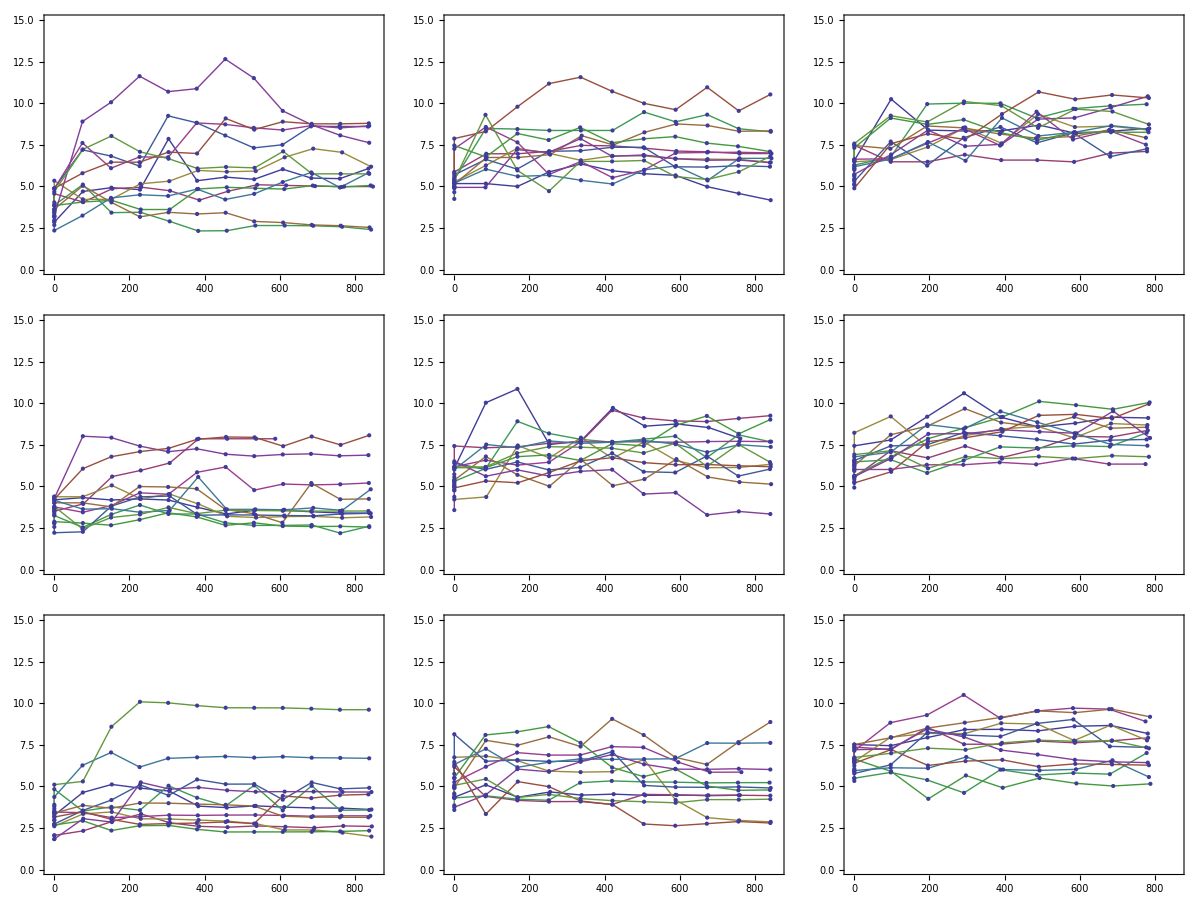

```mathematica
pplots=Table[LP[PValue[#,P⟦Round[(i+1)*3/9]⟧]&/@tmp⟦i⟧,{{-10,860},{0,15}}],{i,1,9}];
grid=Partition[pplots,3]//Transpose//Grid
```

```mathematica
Export["p150e.png",grid]
```

p150e.png

#### Размер популяции: 70, 140, 350.

```mathematica
Vi[Import/@FN["psize/*m1p70*.dev"],P⟦1⟧]
Vi[Import/@FN["psize/*m1p140*.dev"],P⟦1⟧]
Vi[Import/@FN["psize/*m1p350*.dev"],P⟦1⟧]
```

```mathematica
Vi[Import/@FN["psize/*m2p70*.dev"],P⟦2⟧]
Vi[Import/@FN["psize/*m2p140*.dev"],P⟦2⟧]
Vi[Import/@FN["psize/*m2p350*.dev"],P⟦2⟧]
```

```mathematica
Vi[Import/@FN["psize/*m3p70*.dev"],P⟦3⟧]
Vi[Import/@FN["psize/*m3p140*.dev"],P⟦3⟧]
Vi[Import/@FN["psize/*m3p350*.dev"],P⟦3⟧]
```